```mathematica
PaintEdgeWeight2[g_]:=HighlightGraph[Graph[g,
VertexLabels->"Name",
VertexStyle->Red,
VertexLabelStyle->Directive[Red,Medium],
(*EdgeStyle->Table[e->Thickness[1/(ChromaticPolynomial[EdgeDelete[g,e],4])],{e,EdgeList[g]}], *)
(*EdgeLabels->Table[e->ChromaticPolynomial[EdgeDelete[g,e],4]/24,{e,EdgeList[g]}], 
EdgeLabelStyle->Directive[Blue,Medium],*)
PlotLabel->ChromaticPolynomial[g,4], 
GraphLayout->"PlanarEmbedding",
ImageSize->300],
Map[Subgraph[g,#]&,FindClique[g,{4},All]], GraphHighlightStyle->"Dashed"
]
```

```mathematica
PaintEdgeWeight2[g_]:=HighlightGraph[Graph[g,
VertexLabels->"Name",
VertexStyle->Red,
VertexLabelStyle->Directive[Red,Medium],
(*EdgeStyle->Table[e->Thickness[1/(ChromaticPolynomial[EdgeDelete[g,e],4])],{e,EdgeList[g]}], *)
(*EdgeLabels->Table[e->ChromaticPolynomial[EdgeDelete[g,e],4]/24,{e,EdgeList[g]}], 
EdgeLabelStyle->Directive[Blue,Medium],*)
PlotLabel->ChromaticPolynomial[g,4], 
GraphLayout->"PlanarEmbedding",
ImageSize->300],
Map[Subgraph[g,#]&,FindKClan[g, 5]], GraphHighlightStyle->"Dashed"
]
```

```mathematica
Needs["Combinatorica`"]
```

General::compat: Combinatorica Graph and Permutations functionality has been superseded by preloaded functionality. The package now being loaded may conflict with this. Please see the Compatibility Guide for details.

```mathematica
Needspaclet:ref/Needs["Combinatorica`"]
```

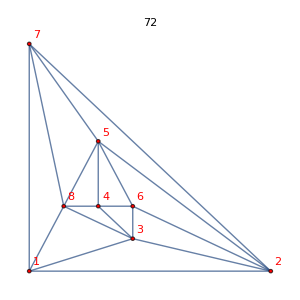
-Graphics--Graphics-

```mathematica
Row[{PaintEdgeWeight2[ReadGrof[6]],PaintEdgeWeight2[ReadGrof[18]]}]
```

```mathematica
With[{g=ReadGrof[2]},Map[EdgeList[Subgraph[g,#]]&,FindKClub[g,1]]]
```

{{1<->2,1<->3,2<->3,1<->5,2<->5,3<->5}}

```mathematica
ChromaticPolynomial[ReadGrof[18],4]
```

72

```mathematica
ChromaticPolynomial[EdgeDelete[ReadGrof[18],{7<->8,8<->3}],4]
```

240

```mathematica
ChromaticPolynomial[EdgeDelete[ReadGrof[18],{5<->8,8<->1}],4]
```

240

```mathematica
Table[PaintEdgeWeight2[ReadGrof[k]],{k,{6,18}}]
```

{-Graphics-,-Graphics-}

```mathematica
Column[
Table[
Row[{PaintEdgeWeight2[ReadGrof[k[[1]] ]],PaintEdgeWeight2[ReadGrof[k[[2]] ]]}],
{k,Take[Select[deps2,Chrom[#[[1]]]-24>Chrom[#[[2]]]&],10]}
]
]
```

-Graphics--Graphics-
-Graphics--Graphics-
-Graphics--Graphics-
-Graphics--Graphics-
-Graphics--Graphics-
-Graphics--Graphics-
-Graphics--Graphics-
-Graphics--Graphics-
-Graphics--Graphics-
-Graphics--Graphics-

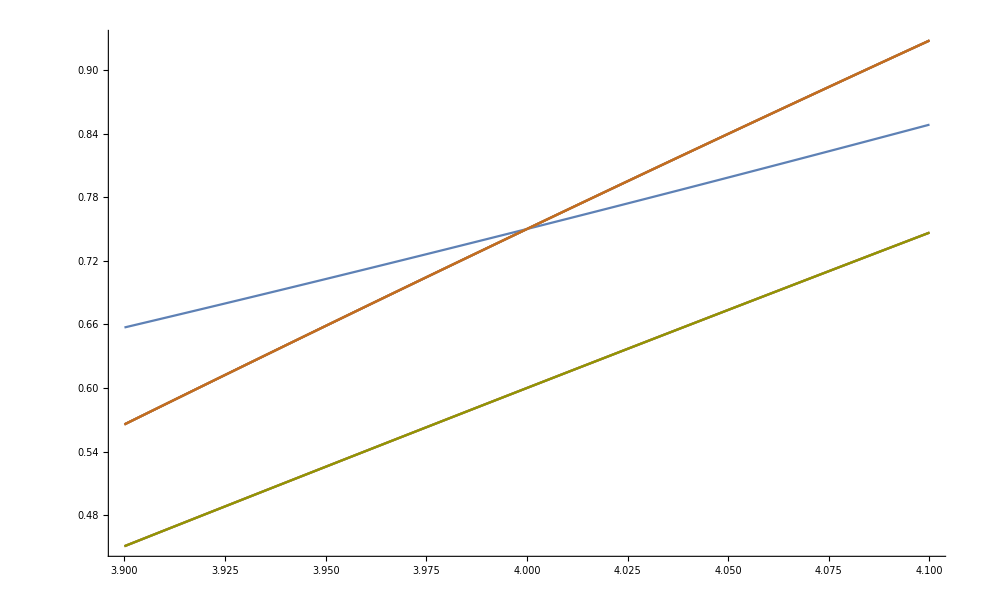

```mathematica
Plot[Tooltip[{(2298 x-7465 x^2+10150 x^3-7670 x^4+3567 x^5-1056 x^6+196 x^7-21 x^8+x^9)/(-664 x+1992 x^2-2432 x^3+1595 x^4-615 x^5+141 x^6-18 x^7+x^8),(-6426 x+23247 x^2-36081 x^3+31900 x^4-17858 x^5+6610 x^6-1627 x^7+258 x^8-24 x^9+x^10)/(1728 x-5886 x^2+8433 x^3-6715 x^4+3277 x^5-1010 x^6+193 x^7-21 x^8+x^9),(-6426 x+23247 x^2-36081 x^3+31900 x^4-17858 x^5+6610 x^6-1627 x^7+258 x^8-24 x^9+x^10)/(1728 x-5886 x^2+8433 x^3-6715 x^4+3277 x^5-1010 x^6+193 x^7-21 x^8+x^9),(-6426 x+23247 x^2-36081 x^3+31900 x^4-17858 x^5+6610 x^6-1627 x^7+258 x^8-24 x^9+x^10)/(1728 x-5886 x^2+8433 x^3-6715 x^4+3277 x^5-1010 x^6+193 x^7-21 x^8+x^9),(-6426 x+23247 x^2-36081 x^3+31900 x^4-17858 x^5+6610 x^6-1627 x^7+258 x^8-24 x^9+x^10)/(1728 x-5886 x^2+8433 x^3-6715 x^4+3277 x^5-1010 x^6+193 x^7-21 x^8+x^9),(-6426 x+23247 x^2-36081 x^3+31900 x^4-17858 x^5+6610 x^6-1627 x^7+258 x^8-24 x^9+x^10)/(1728 x-5886 x^2+8433 x^3-6715 x^4+3277 x^5-1010 x^6+193 x^7-21 x^8+x^9),(-6426 x+23247 x^2-36081 x^3+31900 x^4-17858 x^5+6610 x^6-1627 x^7+258 x^8-24 x^9+x^10)/(1890 x-6345 x^2+8946 x^3-7009 x^4+3369 x^5-1025 x^6+194 x^7-21 x^8+x^9),(-6426 x+23247 x^2-36081 x^3+31900 x^4-17858 x^5+6610 x^6-1627 x^7+258 x^8-24 x^9+x^10)/(1890 x-6345 x^2+8946 x^3-7009 x^4+3369 x^5-1025 x^6+194 x^7-21 x^8+x^9),(-6426 x+23247 x^2-36081 x^3+31900 x^4-17858 x^5+6610 x^6-1627 x^7+258 x^8-24 x^9+x^10)/(1890 x-6345 x^2+8946 x^3-7009 x^4+3369 x^5-1025 x^6+194 x^7-21 x^8+x^9),(-6426 x+23247 x^2-36081 x^3+31900 x^4-17858 x^5+6610 x^6-1627 x^7+258 x^8-24 x^9+x^10)/(1890 x-6345 x^2+8946 x^3-7009 x^4+3369 x^5-1025 x^6+194 x^7-21 x^8+x^9)}],{x,3.9,4.1}]
```

```mathematica
Take[Select[deps2,Chrom[#[[1]]]>Chrom[#[[2]]]&],20]
```

{{6,18},{7,18},{20,40},{11,40},{11,36},{14,40},{15,40},{15,36},{18,50},{19,36},{21,38},{41,97},{41,99},{25,114},{25,88},{25,119},{49,142},{49,143},{26,88},{26,160}}

```mathematica
Table[
ChromaticPolynomial[ReadGrof[k[[2]] ],x]/ChromaticPolynomial[ReadGrof[k[[1]] ],x],
{k,Take[Select[deps2,Chrom[#[[1]]]>Chrom[#[[2]]]&],{11,20}]}
]
```

{(2298 x-7465 x^2+10150 x^3-7670 x^4+3567 x^5-1056 x^6+196 x^7-21 x^8+x^9)/(-664 x+1992 x^2-2432 x^3+1595 x^4-615 x^5+141 x^6-18 x^7+x^8),(-6426 x+23247 x^2-36081 x^3+31900 x^4-17858 x^5+6610 x^6-1627 x^7+258 x^8-24 x^9+x^10)/(1728 x-5886 x^2+8433 x^3-6715 x^4+3277 x^5-1010 x^6+193 x^7-21 x^8+x^9),(-6426 x+23247 x^2-36081 x^3+31900 x^4-17858 x^5+6610 x^6-1627 x^7+258 x^8-24 x^9+x^10)/(1728 x-5886 x^2+8433 x^3-6715 x^4+3277 x^5-1010 x^6+193 x^7-21 x^8+x^9),(-6426 x+23247 x^2-36081 x^3+31900 x^4-17858 x^5+6610 x^6-1627 x^7+258 x^8-24 x^9+x^10)/(1728 x-5886 x^2+8433 x^3-6715 x^4+3277 x^5-1010 x^6+193 x^7-21 x^8+x^9),(-6426 x+23247 x^2-36081 x^3+31900 x^4-17858 x^5+6610 x^6-1627 x^7+258 x^8-24 x^9+x^10)/(1728 x-5886 x^2+8433 x^3-6715 x^4+3277 x^5-1010 x^6+193 x^7-21 x^8+x^9),(-6426 x+23247 x^2-36081 x^3+31900 x^4-17858 x^5+6610 x^6-1627 x^7+258 x^8-24 x^9+x^10)/(1728 x-5886 x^2+8433 x^3-6715 x^4+3277 x^5-1010 x^6+193 x^7-21 x^8+x^9),(-6426 x+23247 x^2-36081 x^3+31900 x^4-17858 x^5+6610 x^6-1627 x^7+258 x^8-24 x^9+x^10)/(1890 x-6345 x^2+8946 x^3-7009 x^4+3369 x^5-1025 x^6+194 x^7-21 x^8+x^9),(-6426 x+23247 x^2-36081 x^3+31900 x^4-17858 x^5+6610 x^6-1627 x^7+258 x^8-24 x^9+x^10)/(1890 x-6345 x^2+8946 x^3-7009 x^4+3369 x^5-1025 x^6+194 x^7-21 x^8+x^9),(-6426 x+23247 x^2-36081 x^3+31900 x^4-17858 x^5+6610 x^6-1627 x^7+258 x^8-24 x^9+x^10)/(1890 x-6345 x^2+8946 x^3-7009 x^4+3369 x^5-1025 x^6+194 x^7-21 x^8+x^9),(-6426 x+23247 x^2-36081 x^3+31900 x^4-17858 x^5+6610 x^6-1627 x^7+258 x^8-24 x^9+x^10)/(1890 x-6345 x^2+8946 x^3-7009 x^4+3369 x^5-1025 x^6+194 x^7-21 x^8+x^9)}

```mathematica
ChromaticPolynomial[ReadGrof[21],3]
```

6

```mathematica
EdgeList[ReadGrof[21]]
```

{1<->2,1<->3,1<->5,1<->7,2<->3,2<->5,2<->8,3<->4,3<->6,3<->7,3<->8,4<->5,4<->6,4<->7,5<->6,5<->7,5<->8,6<->8}

```mathematica
PaintEdgeWeight2[g_]:=HighlightGraph[Graph[g,
VertexLabels->"Name",
VertexStyle->Red,
VertexLabelStyle->Directive[Red,Medium],
(*EdgeStyle->Table[e->Thickness[1/(ChromaticPolynomial[EdgeDelete[g,e],4])],{e,EdgeList[g]}], *)
(*EdgeLabels->Table[e->ChromaticPolynomial[EdgeDelete[g,e],4]/24,{e,EdgeList[g]}], 
EdgeLabelStyle->Directive[Blue,Medium],*)
PlotLabel->ChromaticPolynomial[g,4], 
GraphLayout->"PlanarEmbedding",
ImageSize->300],
Map[Subgraph[g,#]&,FindClique[g, {4},All]], GraphHighlightStyle->"Dashed"
]
```